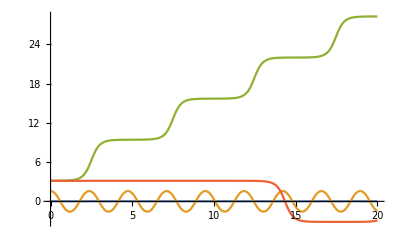

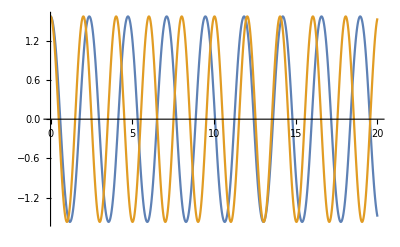

9.81 l Sin[phi0]+1/2 a^2 v^2 Cos[phi0] Sin[phi0]

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{v→-((0.+4.42945 ⅈ) √l)/(a √Cos[phi0])},{v→((0.+4.42945 ⅈ) √l)/(a √Cos[phi0])}}

{{v→-(0.+8.85889 ⅈ)/(√Cos[phi0])},{v→(0.+8.85889 ⅈ)/(√Cos[phi0])}}

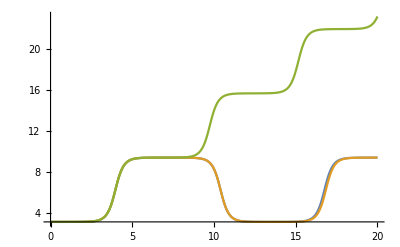

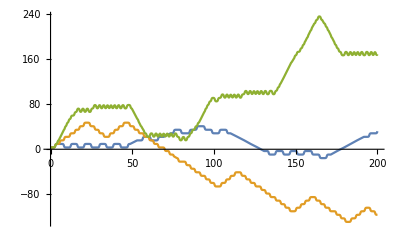

```mathematica
g=9.81;

f[l_,a_,v_, x_, y_]:={phi''[t]==- ((g + a v^2 Cos[v t])/(l)) Sin[phi[t]], phi[0]== x , phi'[0]==y} ;

sol=phi[t] /.NDSolve[f[1,1,0,1,0.001],phi,{t,0,20}];


sol1=phi[t] /.NDSolve[f[1,0,3,0,0.01],phi,{t,0,20}];
sol2=phi[t] /.NDSolve[f[1,0,3,Pi/2,0.01],phi,{t,0,20}];
sol3=phi[t] /.NDSolve[f[1,0,3,Pi,0.01],phi,{t,0,20}];
sol4=phi[t] /.NDSolve[f[1,0,3,Pi,0],phi,{t,0,20}];


Plot[{sol1,sol2,sol3,sol4} ,{t,0,20} ]

eq2[l_]:={y''[t]==-(g/l)(y[t]), y'[0]==0.01, y[0]==Pi/2};
soleq2=y[t]/.DSolve[eq2[1],y[t],t];

Plot[{sol2,soleq2},{t,0,20}]

Veff[l_,a_,v_,phi0]:=-g l Cos[phi0] + ( (a^2)(v^2)/4 ) Sin[phi0]^2;

 condMin=D[Veff[l,a,v,phi0],phi0]
min[l_,a_]=NSolve[ Simplify[condMin]==0 ,v]
nubarra=min[1,0.5]

pend1=phi[t]/.NDSolve[f[1,0.01,0.001,Pi,0.0001],phi,{t,0,20}];
pend2=phi[t]/.NDSolve[f[1,0.01,0.01,Pi,0.0001],phi,{t,0,20}];
pend3=phi[t]/.NDSolve[f[1,0.01,0.1,Pi,0.0001],phi,{t,0,20}];

Plot[{pend1,pend2,pend3},{t,0,20}]

pend4=phi[t]/.NDSolve[f[0.5,0.01,0.05,Pi,0.0001],phi,{t,0,200}];
pend5=phi[t]/.NDSolve[f[0.5,0.01,0.5489,Pi,0.0001],phi,{t,0,200}];
pend6=phi[t]/.NDSolve[f[0.5,0.01,4.907,Pi,0.0001],phi,{t,0,200}];
(*pend7=phi[t]/.DSolve[f[0.5,0.01,nubarra,Pi,0.0001],phi,{t,0,200}];*)

Plot[{pend4,pend5,pend6(*pend7*)},{t,0,200}]
```